## Matrix Element calculation (including time evolution)

```mathematica
Clear[n, η]
```

```mathematica
hbar = 1.0545718×10^-34;m = 6.94 * 1.660539 10^-27 ; ω = 10^6;ωt=4*10^7; t = 10^-7; n = 2;
nmax = 15; τ = 27.102 10^-9;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 6.94 * 1.660539 10^-27 ; 
Dr[n_,nt_, η_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η 1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η 1)^2]Exp[-η^2/2];
Drw[n_,nt_, η_, θ_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  Cos[θ])^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  Cos[θ])^2]Exp[-(η  Cos[θ])^2/2];
CustomDelta[x_] := Piecewise[{{1, x ==0}, {0, x ≠0}}]
(*UP[ω_,x_,xt_,t_]:= ((m ω)/(2 Pi ⅈ hbar Sin[ω t]))^(1/2) Exp[ⅈ/(2 hbar Sin[ω t])((x^2+ xt^2)Cos[ω t]-2 x xt)];*)
U[ω_, ωt_,n_, nt_, t_]:= CustomDelta[nt-n-2] Sqrt[(n+1)(n+2)]/4(Max[ω, ωt]^2-Min[ω, ωt]^2)/Max[ω, ωt] t+ CustomDelta[nt-n+2] Sqrt[(n - 2+1)(n - 2+2)]/4(Max[ω, ωt]^2-Min[ω, ωt]^2)/Max[ω, ωt] t + CustomDelta[n-nt]*Sqrt[((1- Sqrt[(n+1)(n+2)]/4(Max[ω, ωt]^2-Min[ω, ωt]^2)/Max[ω, ωt] t)^2 - (Sqrt[(n - 2+1)(n - 2+2)]/4(Max[ω, ωt]^2-Min[ω, ωt]^2)/Max[ω, ωt] t)^2)]
M[n_,nt_] :=NIntegrate[Sin[θ]/2 Abs[Sum[√((Min[n,m]!)/((Min[n,m]+Abs[m-n])!))(ⅈ η Cos[θ] )^Abs[m-n] LaguerreL[Min[n,m],Abs[m-n],(η Cos[θ])^2]Exp[-(η Cos[θ])^2/2] Dr[m,nt],{m,0,nmax}]]^2,{θ,0, Pi}]
```

```mathematica
Umat = Table[U[1*10^5, 2*10^5, n, nt, 10^-7],{n,0,nmax},{nt,0,nmax}]//N
```

{{0.994697,0.,0.0053033,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.990814,0.,0.00918559,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0053033,0.,0.986995,0.,0.0129904,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.00918559,0.,0.983187,0.,0.0167705,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.0129904,0.,0.979374,0.,0.0205396,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.0167705,0.,0.975553,0.,0.0243028,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.0205396,0.,0.971721,0.,0.0280624,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.0243028,0.,0.967875,0.,0.0318198,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.0280624,0.,0.964016,0.,0.0355756,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.0318198,0.,0.960143,0.,0.0393303,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0355756,0.,0.956254,0.,0.0430842,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0393303,0.,0.952351,0.,0.0468375,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0430842,0.,0.948432,0.,0.0505903,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0468375,0.,0.944497,0.,0.0543427},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0505903,0.,0.940546,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0543427,0.,0.936578}}

```mathematica
{{0.9946966991411009,0.,0.005303300858899107,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.9908144134645631,0.,0.009185586535436916,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.005303300858899107,0.,0.9869953712588864,0.,0.012990381056766578,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.009185586535436916,U0.`,0.9831865821590037,0.,0.01677050983124842,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.012990381056766578,0.,0.979374255934427,0.,0.020539595906443726,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.01677050983124842,0.,0.9755530840307671,0.,0.024302777619029475,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.020539595906443726,0.,0.9717205175349499,0.,0.02806243040080456,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.024302777619029475,0.,0.9678751286675419,0.,0.03181980515339464,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.02806243040080456,0.,0.9640160152436325,0.,0.03557562367689427,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.03181980515339464,0.,0.9601425474309732,0.,0.03933033180638069,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.03557562367689427,0.,0.9562542472072632,0.,0.04308421984903521,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.03933033180638069,0.,0.9523507258484261,0.,0.04683748498798799,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.04308421984903521,0.,0.9484316492377085,0.,0.050590265862120155,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.04683748498798799,0.,0.9444967175186895,0.,0.054342662798210394},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.050590265862120155,0.,0.9405456525941617,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.054342662798210394,0.,0.9365781901322868}}
```

```mathematica
Decay Paths
```

```mathematica
(*from LambDickeParams_Singe.py @532nm and @10**7 lattice beam intensity *)
(*levels=["6s 2 S 1/2","7p 2 P ?3/2","7s 2 S 1/2","6p 2 P ?1/2","6p 2 P ?3/2","5d 2 D 3/2","5d 2 D 5/2"]*)
(*decays=[l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34]*)
omegas = {93404.36151476773,58312.21388517295,52564.18722654877,96487.56959133178,149378.74074871602,114323.656390064,134446.8575802304};
etas = {0.697646827167697,0.14448683087878345,0.17095247621856766,0.35533728030290285,0.10383570605450117,0.3729352538139725,0.06952852571696208,0.07198024772090308,0.19467123685222815,0.21390857630773225,0.23003214721947357};
omega[n_]:= omegas[[n]]
eta[n_]:= etas[[n]]
eta[3]
```

0.170952

```mathematica
eta[5]
```

0.372935

```mathematica
Dr[1,2, eta[2]]
```

0.+0.234775 ⅈ

```mathematica
Dr[1,5, eta[2]]
```

0.000381935+0. ⅈ

```mathematica
τ = 10^-7
```

1/10000000

```mathematica
θ1 = 1; θ2= 1;θ3= 1;t1 = 10^-6;t2 = 10^-6;t3 = 10^-6
```

```mathematica
Clear[θ1,θ2,θ3,t1,t2,t3]
```

```mathematica
UA[n_,nt_] := Sum[Sum[ Sum[ 

NIntegrate[Exp[-t1/τ]Exp[-t2/τ]Exp[-t3/τ]
1/2 Sin[θ1] 1/2 Sin[θ2] 1/2 Sin[θ3]
Abs[Drw[n,k, eta[4], θ3]  U[omega[4], omega[1],k, n, t3]  Drw[k,l, eta[11], θ2]  U[omega[3], omega[4],l, k, t2]   Drw[l,m, eta[2], θ1]  U[omega[2], omega[3],m, l, t1] Dr[m,nt, eta[1]]
]^2
,{θ3,0,  Pi},{θ2,0, Pi},{θ1,0, Pi}
,{t3,0, 1},{t2,0, 1},{t1,0, 1}]
,{m,0,3}],{l,0,3}], {k,0,3}]
```

```mathematica
UA[1,2]
```

Part::partd: Part specification eta⟦2⟧ is longer than depth of object.

Part::partd: Part specification eta⟦4⟧ is longer than depth of object.

-((ⅇ^(-Symbol^2/2-η^2/2) (ⅈ Symbol)^Abs[nt] η^2 √((Min[0,nt]!)/((Abs[nt]+Min[0,nt])!)) LaguerreL[Min[0,nt],Abs[nt],Symbol^2] (Max[{93404.4,58312.2,52564.2,96487.6,149379.,114324.,134447.}[0],{93404.4,58312.2,52564.2,96487.6,149379.,114324.,134447.}[2]]^2-Min[{93404.4,58312.2,52564.2,96487.6,149379.,114324.,134447.}[0],{93404.4,58312.2,52564.2,96487.6,149379.,114324.,134447.}[2]]^2))/(40000000 Max[{93404.4,58312.2,52564.2,96487.6,149379.,114324.,134447.}[0],{93404.4,58312.2,52564.2,96487.6,149379.,114324.,134447.}[2]]))+1/2 ⅇ^(-η^2/2-eta⟦2⟧^2/2) (2-4 η^2+η^4) √((Min[2,nt]!)/((Abs[-2+nt]+Min[2,nt])!)) LaguerreL[Min[2,nt],Abs[-2+nt],eta⟦2⟧^2] (ⅈ eta⟦2⟧)^Abs[-2+nt]-(ⅇ^(-η^2/2-eta⟦4⟧^2/2) η^2 (12-8 η^2+η^4) √((Min[4,nt]!)/((Abs[-4+nt]+Min[4,nt])!)) LaguerreL[Min[4,nt],Abs[-4+nt],eta⟦4⟧^2] (Max[{93404.4,58312.2,52564.2,96487.6,149379.,114324.,134447.}[2],{93404.4,58312.2,52564.2,96487.6,149379.,114324.,134447.}[4]]^2-Min[{93404.4,58312.2,52564.2,96487.6,149379.,114324.,134447.}[2],{93404.4,58312.2,52564.2,96487.6,149379.,114324.,134447.}[4]]^2) (ⅈ eta⟦4⟧)^Abs[-4+nt])/(80000000 Max[{93404.4,58312.2,52564.2,96487.6,149379.,114324.,134447.}[2],{93404.4,58312.2,52564.2,96487.6,149379.,114324.,134447.}[4]])

```mathematica
Dr[1,1,0.14448683087878345,1]
```

Dr[1,1,0.144487,1]

```mathematica
Dr[1,1]
```

0.940991+0. ⅈ

```mathematica
M [3,3]
```

0.708382

```mathematica
DrMat = Table[Dr[n,nt],{n,0,nmax },{nt,0,nmax}] ;
```

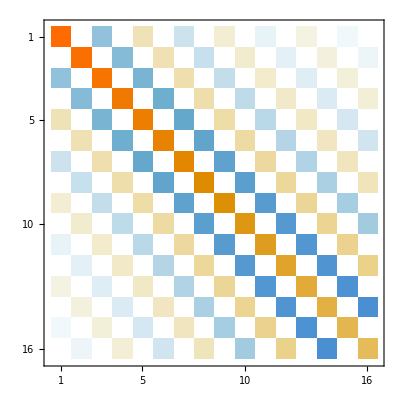

```mathematica
MatrixPlot[DrMat]
```

```mathematica
Table[ Sum[Abs[DrMat[[j,m]]]^2,{m,1,11}],{j,1,16}]
```

{1.,1.,1.,1.,1.,1.,0.999997,0.99983,0.994862,0.924839,0.58221,0.404284,0.0851931,0.00828945,0.000476312,0.0000184922}

```mathematica
Mat = Table[M[n,nt],{n,0,nmax},{nt,0,nmax}]
```

```mathematica
{{0.9491320992511889,0.04849415514248862+omega0.` ⅈ,0.002284864798217879,0.00008614724872031362+0. ⅈ,2.662572638490946*^-6,6.939473490448287*^-8+0. ⅈ,1.560623269726821*^-9,3.0836646239924205*^-11+0. ⅈ,5.43085194085202*^-13,8.624538310826293*^-15+0. ⅈ,1.2468329765501838*^-16,1.6540117958382301*^-18+0. ⅈ,2.0269794493746398*^-20,2.308043286964348*^-22+0. ⅈ,2.4540858442771483*^-24,2.4472668796452588*^-26+0. ⅈ},{0.04849415514248862+0. ⅈ,0.8567135185626467,0.08810729283826771+0. ⅈ,0.006348361192885722,0.00032363538744785084+0. ⅈ,0.000012628279583025285,3.978567867137921*^-7+0. ⅈ,1.0496994522281502*^-8,2.3808142765881234*^-10+0. ⅈ,4.733771890156658*^-12,8.376991128491533*^-14+0. ⅈ,1.3353712522322803*^-15,1.9364666937098495*^-17+0. ⅈ,2.5754077394473265*^-19,3.1629129181970904*^-21+0. ⅈ,3.6080874919917274*^-23},{0.002284864798217879,0.08810729283826775+0. ⅈ,0.7769863351145976,0.12006841402216877+0. ⅈ,0.011756055636066208,0.0007597342232802202+0. ⅈ,0.000035931513984690786,1.3304536937518926*^-6+0. ⅈ,4.0342438526423*^-8,1.0339107866306715*^-9+0. ⅈ,2.2922212449453307*^-11,4.474961605420183*^-13+0. ⅈ,7.800880055709357*^-15,1.228018718274917*^-16+0. ⅈ,1.76193645272597*^-18,2.3219902554486423*^-20+0. ⅈ},{0.0000861472487203136+0. ⅈ,0.006348361192885723,0.12006841402216878+0. ⅈ,0.7083832258193168,0.14546694462863174+0. ⅈ,0.01813740178846393,0.0014264902300288916+0. ⅈ,0.00007950593549147223,3.3894497739736272*^-6+0. ⅈ,1.1627565010189766*^-7,3.3257024616856775*^-9+0. ⅈ,8.13934486250024*^-11,1.7384980058621718*^-12+0. ⅈ,3.291131789561089*^-14,5.590935476237426*^-16+0. ⅈ,8.61002928554612*^-18},{2.662572638490947*^-6,0.0003236353874478509+0. ⅈ,0.01175605563606621,0.14546694462863174+0. ⅈ,0.6495044640135261,0.16526621367490887+0. ⅈ,0.02517855408927413,0.0023431270908363935+0. ⅈ,0.0001507696099317991,7.284973864198213*^-6+0. ⅈ,2.79255806963041*^-7,8.82498784733771*^-9+0. ⅈ,2.3645821560810895*^-10,5.487426960170934*^-12+0. ⅈ,1.1214539628333965*^-13,2.0454605757616387*^-15+0. ⅈ},{6.939473490448287*^-8+0. ⅈ,0.00001262827958302529+0. ⅈ,0.0007597342232802203+0. ⅈ,0.01813740178846393+0. ⅈ,0.16526621367490885+0. ⅈ,0.5991023220199286+0. ⅈ,0.18031579888163166+0. ⅈ,0.03261584984346716+0. ⅈ,0.0035181733625980097+0. ⅈ,0.00025728084124261515+0. ⅈ,0.00001391648820294249+0. ⅈ,5.901551943729788*^-7+0. ⅈ,2.0436180962220696*^-8+0. ⅈ,5.953243893677938*^-10+0. ⅈ,1.4921849224101416*^-11+0. ⅈ,3.2755545561454825*^-13+0. ⅈ},{1.5606232697268207*^-9+0. ⅈ,3.9785678671379215*^-7+0. ⅈ,0.000035931513984690786+0. ⅈ,0.0014264902300288919+0. ⅈ,0.02517855408927412+0. ⅈ,0.1803157988816317+0. ⅈ,0.556066752135703+0. ⅈ,0.1913628240406852+0. ⅈ,0.04022990634894541+0. ⅈ,0.004951342257692971+0. ⅈ,0.00040645649307887696+0. ⅈ,0.000024366769532050712+0. ⅈ,1.1337187715118237*^-6+0. ⅈ,4.272112241123561*^-8+0. ⅈ,1.3450382437947102*^-9+0. ⅈ,3.623262783015614*^-11+0. ⅈ},{3.083664623992419*^-11+0. ⅈ,1.0496994522281497*^-8+0. ⅈ,1.3304536937518915*^-6+0. ⅈ,0.00007950593549147219+0. ⅈ,0.0023431270908363918+0. ⅈ,0.03261584984346715+0. ⅈ,0.1913628240406851+0. ⅈ,0.519412252657044+0. ⅈ,0.19906228672475654+0. ⅈ,0.047840283354024106+0. ⅈ,0.006635186595085387+0. ⅈ,0.0006053453470446683+0. ⅈ,0.00003988990768323648+0. ⅈ,2.022217587656307*^-6+0. ⅈ,8.243089661165882*^-8+0. ⅈ,2.7915015376734374*^-9+0. ⅈ},{5.430851940852016*^-13+0. ⅈ,2.380814276588121*^-10+0. ⅈ,4.034243852642298*^-8+0. ⅈ,3.389449773973625*^-6+0. ⅈ,0.00015076960993179898+0. ⅈ,0.003518173362598007+0. ⅈ,0.04022990634894536+0. ⅈ,0.19906228672475437+0. ⅈ,0.48826583169350235+0. ⅈ,0.20398648965880228+0. ⅈ,0.0553006646526801+0. ⅈ,0.008556550216213467+0. ⅈ,0.0008604495973734009+0. ⅈ,0.00006189485714746931+0. ⅈ,3.398489696542642*^-6+0. ⅈ,1.4919932061242852*^-7+0. ⅈ},{8.624538310826284*^-15+0. ⅈ,4.7337718901566555*^-12+0. ⅈ,1.033910786630671*^-9+0. ⅈ,1.162756501018977*^-7+0. ⅈ,7.2849738641982444*^-6+0. ⅈ,0.0002572808412426203+0. ⅈ,0.004951342257693365+0. ⅈ,0.04784028335403879+0. ⅈ,0.2039864896586216+0. ⅈ,0.4618559872660948+0. ⅈ,0.20663364390414815+0. ⅈ,0.0624945177487135+0. ⅈ,0.010697828994725697+0. ⅈ,0.0011776011849557498+0. ⅈ,0.00009191093224995167+0. ⅈ,5.447237356027749*^-6+0. ⅈ},{1.246832976550177*^-16+0. ⅈ,8.376991128491412*^-14+0. ⅈ,2.2922212449452344*^-11+0. ⅈ,3.325702461685249*^-9+0. ⅈ,2.792558069629253*^-7+0. ⅈ,0.000013916488202923153+0. ⅈ,0.00040645649307690176+0. ⅈ,0.006635186594967826+0. ⅈ,0.05530066464908692+0. ⅈ,0.206633643794784+0. ⅈ,0.43950262230279524+0. ⅈ,0.20743573798915366+0. ⅈ,0.0693310201473116+0. ⅈ,0.013038540035871304+0. ⅈ,0.0015611761531738378+0. ⅈ,0.00013206624252976734+0. ⅈ},{1.6540117958389177*^-18+0. ⅈ,1.3353712522338032*^-15+0. ⅈ,4.474961605434453*^-13+0. ⅈ,8.139344862574535*^-11+0. ⅈ,8.824987847574442*^-9+0. ⅈ,5.901551944209195*^-7+0. ⅈ,0.00002436676953824704+0. ⅈ,0.0006053453475432553+0. ⅈ,0.008556550239478225+0. ⅈ,0.062494518289891686+0. ⅈ,0.2074357326975721+0. ⅈ,0.42060730779148103+0. ⅈ,0.2067641670301822+0. ⅈ,0.07575108126172539+0. ⅈ,0.015536033584025739+0. ⅈ,0.0020332869443685894+0. ⅈ},{2.0269794493112316*^-20+0. ⅈ,1.9364666935553098*^-17+0. ⅈ,7.800880054096323*^-15+0. ⅈ,1.7384980049143113*^-12+0. ⅈ,2.364582152613659*^-10+0. ⅈ,2.043618087978471*^-8+0. ⅈ,1.133718758606849*^-6+0. ⅈ,0.000039889906364979553+0. ⅈ,0.0008604495123062294+0. ⅈ,0.010697825726992651+0. ⅈ,0.06933095483619535+0. ⅈ,0.20676286570620797+0. ⅈ,0.4046184905192288+0. ⅈ,0.20503927950452683+0. ⅈ,0.0813855094513608+0. ⅈ,0.01858533474404928+0. ⅈ},{2.308043291217634*^-22+0. ⅈ,2.5754077507882314*^-19+0. ⅈ,1.2280187313392064*^-16+0. ⅈ,3.29113187519671*^-14+0. ⅈ,5.487427314288523*^-12+0. ⅈ,5.953244861611557*^-10+0. ⅈ,4.27211402265578*^-8+0. ⅈ,2.0222197941851393*^-6+0. ⅈ,0.0000618950376759689+0. ⅈ,0.001177610548167236+0. ⅈ,0.01303882166054936+0. ⅈ,0.07575520593786125+0. ⅈ,0.2050098980211765+0. ⅈ,0.38989100332211174+0. ⅈ,0.2011298875925387+0. ⅈ,0.09141165325063151+0. ⅈ},{2.4540856494627524*^-24+0. ⅈ,3.1629123534405935*^-21+0. ⅈ,1.7619357400737838*^-18+0. ⅈ,5.590930312965466*^-16+0. ⅈ,1.1214515769678943*^-13+0. ⅈ,1.4921775351237757*^-11+0. ⅈ,1.3450225708339092*^-9+0. ⅈ,8.242860637948016*^-8+0. ⅈ,3.3982612490315084*^-6+0. ⅈ,0.00009189573864897433+0. ⅈ,0.0015605304319292951+0. ⅈ,0.015519557169037912+0. ⅈ,0.0811648077945347+0. ⅈ,0.19849988208432315+0. ⅈ,0.3600537452482166+0. ⅈ,0.23471272736790794+0. ⅈ},{2.4472721744499754*^-26+0. ⅈ,3.608104107779635*^-23+0. ⅈ,2.3220131044312444*^-20+0. ⅈ,8.610211115145456*^-18+0. ⅈ,2.045553736000601*^-15+0. ⅈ,3.275878074339532*^-13+0. ⅈ,3.624043658684086*^-11+0. ⅈ,2.79282341667055*^-9+0. ⅈ,1.493557265325675*^-7+0. ⅈ,5.459974667775302*^-6+0. ⅈ,0.00013275898278266012+0. ⅈ,0.002057170052968221+0. ⅈ,0.019055529320124078+0. ⅈ,0.09579621337427285+0. ⅈ,0.22211434036149175+0. ⅈ,0.20984660752741177+0. ⅈ}}
```

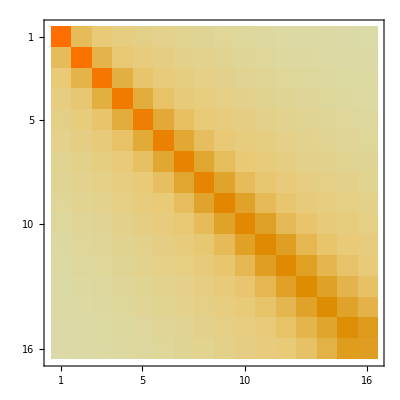

```mathematica
MatrixPlot[Mat]
```

```mathematica
<
```

```mathematica
Table[ Sum[Mat[[j,m]],{m,1,11}],{j,1,16}]
```

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.999999+0. ⅈ,0.999974+0. ⅈ,0.999353+0. ⅈ,0.990518+0. ⅈ,0.925532+0. ⅈ,0.708493+0. ⅈ,0.279117+0. ⅈ,0.0809303+0. ⅈ,0.0142804+0. ⅈ,0.00165591+0. ⅈ,0.000138371+0. ⅈ}

```mathematica
{0.9500066076371911+0. ⅈ,0.9981858353884894+0. ⅈ,0.9999252554603134+0. ⅈ,0.9999975389684228+0. ⅈ,0.9999999137599004+0. ⅈ,0.9999989443099998+0. ⅈ,0.9999639056062806+0. ⅈ,0.9991850718498525+0. ⅈ,0.9869398839062721+0. ⅈ,0.8466419397926749+0. ⅈ,0.11540074126484189+0. ⅈ}
Table[ Sum[M[j,m],{m,1,40}],{j,1,40}]
```

{0.950007+0. ⅈ,0.998186+0. ⅈ,0.999925+0. ⅈ,0.999998+0. ⅈ,1.+0. ⅈ,0.999999+0. ⅈ,0.999964+0. ⅈ,0.999185+0. ⅈ,0.98694+0. ⅈ,0.846642+0. ⅈ,0.115401+0. ⅈ}

{0.980684,0.999521,0.999992,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999894,0.993787,0.84998,0.149262,0.00692783,0.000149055,1.88655×10^-6,1.59863×10^-8,9.83276×10^-11,4.63835×10^-13,1.74623×10^-15,5.40682×10^-18,1.40948×10^-20,3.15211×10^-23,6.1407×10^-26,1.05545×10^-28,1.61778×10^-31,2.23173×10^-34,2.79275×10^-37,3.1921×10^-40,3.3527×10^-43,3.25314×10^-46,2.92995×10^-49,2.45986×10^-52,1.93247×10^-55,1.42548×10^-58,9.90425×10^-62}

```mathematica
Adiabatic elimination of state 2
```

```mathematica
α = 0.6;
```

```mathematica
Eigenvalues[Mat]
```

{0.976214,0.897995,0.77029,0.605649,0.4216,-0.396012,-0.386373,-0.342232,-0.329749,-0.238988,0.234944,-0.227032,0.114543,-0.102563,-0.0745253,0.0575847}

```mathematica
MatEl2 = Mat.Inverse[IdentityMatrix[nmax+1]-(1-α)*Mat]
```

{{1.53376+0. ⅈ,0.119664+0. ⅈ,0.011568+0. ⅈ,0.00141105+0. ⅈ,0.000214689+0. ⅈ,0.0000384659+0. ⅈ,7.80744×10^-6+0. ⅈ,1.75271×10^-6+0. ⅈ,4.27811×10^-7+0. ⅈ,1.12096×10^-7+0. ⅈ,3.12233×10^-8+0. ⅈ,9.17406×10^-9+0. ⅈ,2.82546×10^-9+0. ⅈ,9.06342×10^-10+0. ⅈ,2.97959×10^-10+0. ⅈ,9.98857×10^-11+0. ⅈ},{0.119664+0. ⅈ,1.31757+0. ⅈ,0.197289+0. ⅈ,0.0270965+0. ⅈ,0.00411901+0. ⅈ,0.000735629+0. ⅈ,0.000149375+0. ⅈ,0.0000335367+0. ⅈ,8.18554×10^-6+0. ⅈ,2.1448×10^-6+0. ⅈ,5.97413×10^-7+0. ⅈ,1.75532×10^-7+0. ⅈ,5.40611×10^-8+0. ⅈ,1.73415×10^-8+0. ⅈ,5.70101×10^-9+0. ⅈ,1.91117×10^-9+0. ⅈ},{0.011568+0. ⅈ,0.197289+0. ⅈ,1.15514+0. ⅈ,0.249273+0. ⅈ,0.0435677+0. ⅈ,0.00778391+0. ⅈ,0.00157349+0. ⅈ,0.000353458+0. ⅈ,0.0000862857+0. ⅈ,0.0000226076+0. ⅈ,6.2971×10^-6+0. ⅈ,1.85023×10^-6+0. ⅈ,5.69839×10^-7+0. ⅈ,1.82791×10^-7+0. ⅈ,6.00924×10^-8+0. ⅈ,2.0145×10^-8+0. ⅈ},{0.00141105+0. ⅈ,0.0270965+0. ⅈ,0.249273+0. ⅈ,1.02898+0. ⅈ,0.284501+0. ⅈ,0.0597015+0. ⅈ,0.012097+0. ⅈ,0.00270102+0. ⅈ,0.000659778+0. ⅈ,0.000172916+0. ⅈ,0.0000481599+0. ⅈ,0.0000141503+0. ⅈ,4.3581×10^-6+0. ⅈ,1.39798×10^-6+0. ⅈ,4.59583×10^-7+0. ⅈ,1.54068×10^-7+0. ⅈ},{0.000214689+0. ⅈ,0.00411901+0. ⅈ,0.0435677+0. ⅈ,0.284501+0. ⅈ,0.928685+0. ⅈ,0.308232+0. ⅈ,0.0749534+0. ⅈ,0.0168222+0. ⅈ,0.00407693+0. ⅈ,0.0010692+0. ⅈ,0.00029792+0. ⅈ,0.0000875251+0. ⅈ,0.0000269559+0. ⅈ,8.64694×10^-6+0. ⅈ,2.84267×10^-6+0. ⅈ,9.52957×10^-7+0. ⅈ},{0.0000384659+0. ⅈ,0.000735629+0. ⅈ,0.00778391+0. ⅈ,0.0597015+0. ⅈ,0.308232+0. ⅈ,0.847575+0. ⅈ,0.323789+0. ⅈ,0.0891104+0. ⅈ,0.0217891+0. ⅈ,0.00565759+0. ⅈ,0.00157742+0. ⅈ,0.000463727+0. ⅈ,0.000142799+0. ⅈ,0.0000458053+0. ⅈ,0.0000150587+0. ⅈ,5.04818×10^-6+0. ⅈ},{7.80744×10^-6+0. ⅈ,0.000149375+0. ⅈ,0.00157349+0. ⅈ,0.012097+0. ⅈ,0.0749534+0. ⅈ,0.323789+0. ⅈ,0.781146+0. ⅈ,0.333381+0. ⅈ,0.102114+0. ⅈ,0.0268783+0. ⅈ,0.00740219+0. ⅈ,0.00217713+0. ⅈ,0.000671046+0. ⅈ,0.000215215+0. ⅈ,0.0000707481+0. ⅈ,0.0000237177+0. ⅈ},{1.75271×10^-6+0. ⅈ,0.0000335367+0. ⅈ,0.000353458+0. ⅈ,0.00270102+0. ⅈ,0.0168222+0. ⅈ,0.0891104+0. ⅈ,0.333381+0. ⅈ,0.726216+0. ⅈ,0.338537+0. ⅈ,0.113976+0. ⅈ,0.032007+0. ⅈ,0.0092747+0. ⅈ,0.00285918+0. ⅈ,0.000918171+0. ⅈ,0.000301778+0. ⅈ,0.000101158+0. ⅈ},{4.27811×10^-7+0. ⅈ,8.18554×10^-6+0. ⅈ,0.0000862857+0. ⅈ,0.000659778+0. ⅈ,0.00407693+0. ⅈ,0.0217891+0. ⅈ,0.102114+0. ⅈ,0.338537+0. ⅈ,0.680455+0. ⅈ,0.340357+0. ⅈ,0.12474+0. ⅈ,0.0371188+0. ⅈ,0.0112431+0. ⅈ,0.00360923+0. ⅈ,0.00118832+0. ⅈ,0.000398258+0. ⅈ},{1.12096×10^-7+0. ⅈ,2.1448×10^-6+0. ⅈ,0.0000226076+0. ⅈ,0.000172916+0. ⅈ,0.0010692+0. ⅈ,0.00565759+0. ⅈ,0.0268783+0. ⅈ,0.113976+0. ⅈ,0.340357+0. ⅈ,0.642108+0. ⅈ,0.339651+0. ⅈ,0.134461+0. ⅈ,0.0421701+0. ⅈ,0.0132639+0. ⅈ,0.004362+0. ⅈ,0.00146517+0. ⅈ},{3.12233×10^-8+0. ⅈ,5.97413×10^-7+0. ⅈ,6.2971×10^-6+0. ⅈ,0.0000481599+0. ⅈ,0.00029792+0. ⅈ,0.00157742+0. ⅈ,0.00740219+0. ⅈ,0.032007+0. ⅈ,0.12474+0. ⅈ,0.339651+0. ⅈ,0.609819+0. ⅈ,0.337029+0. ⅈ,0.143177+0. ⅈ,0.0470737+0. ⅈ,0.0151263+0. ⅈ,0.00507051+0. ⅈ},{9.17406×10^-9+0. ⅈ,1.75532×10^-7+0. ⅈ,1.85023×10^-6+0. ⅈ,0.0000141503+0. ⅈ,0.0000875251+0. ⅈ,0.000463727+0. ⅈ,0.00217713+0. ⅈ,0.0092747+0. ⅈ,0.0371188+0. ⅈ,0.134461+0. ⅈ,0.337029+0. ⅈ,0.582496+0. ⅈ,0.332906+0. ⅈ,0.150741+0. ⅈ,0.0511951+0. ⅈ,0.0167219+0. ⅈ},{2.82546×10^-9+0. ⅈ,5.4061×10^-8+0. ⅈ,5.69839×10^-7+0. ⅈ,4.35809×10^-6+0. ⅈ,0.0000269559+0. ⅈ,0.000142799+0. ⅈ,0.000671046+0. ⅈ,0.00285918+0. ⅈ,0.011243+0. ⅈ,0.0421701+0. ⅈ,0.143177+0. ⅈ,0.332905+0. ⅈ,0.559072+0. ⅈ,0.327168+0. ⅈ,0.155229+0. ⅈ,0.0540973+0. ⅈ},{9.06442×10^-10+0. ⅈ,1.73435×10^-8+0. ⅈ,1.82811×10^-7+0. ⅈ,1.39813×10^-6+0. ⅈ,8.6479×10^-6+0. ⅈ,0.0000458103+0. ⅈ,0.000215239+0. ⅈ,0.000918273+0. ⅈ,0.00360963+0. ⅈ,0.0132654+0. ⅈ,0.0470787+0. ⅈ,0.150763+0. ⅈ,0.327189+0. ⅈ,0.536178+0. ⅈ,0.315159+0. ⅈ,0.156281+0. ⅈ},{2.97147×10^-10+0. ⅈ,5.68549×10^-9+0. ⅈ,5.99287×10^-8+0. ⅈ,4.58331×10^-7+0. ⅈ,2.83493×10^-6+0. ⅈ,0.0000150177+0. ⅈ,0.0000705555+0. ⅈ,0.000300957+0. ⅈ,0.00118509+0. ⅈ,0.0043501+0. ⅈ,0.0150845+0. ⅈ,0.0510627+0. ⅈ,0.15487+0. ⅈ,0.312741+0. ⅈ,0.489533+0. ⅈ,0.320177+0. ⅈ},{1.00593×10^-10+0. ⅈ,1.92471×10^-9+0. ⅈ,2.02877×10^-8+0. ⅈ,1.55159×10^-7+0. ⅈ,9.59707×10^-7+0. ⅈ,5.08394×10^-6+0. ⅈ,0.0000238858+0. ⅈ,0.000101874+0. ⅈ,0.00040107+0. ⅈ,0.00147565+0. ⅈ,0.00510743+0. ⅈ,0.0168175+0. ⅈ,0.0544674+0. ⅈ,0.160194+0. ⅈ,0.304466+0. ⅈ,0.26713+0. ⅈ}}

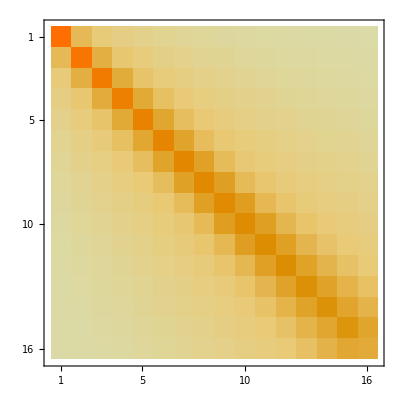

```mathematica
MatrixPlot[MatEl2]
```

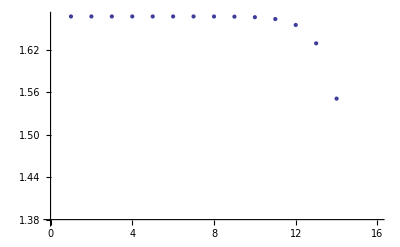

```mathematica
ListPlot[Table[ Sum[MatEl2 [[j,m]],{m,1,16}],{j,1,16}]]
```